## Slučajni vektorji

1. Dana je tabela (1 | -1 | 3
4 | 1 | 5).
	a) Zapišite tabelo v obliki matrike. 
	b) Izračunajte vrstične in stolpčne vsote.

```mathematica
ClearAll["Global`*"]
(* a) *)
tab = {{1,-1,3},{4,1,5}};
MatrixForm[tab]
```

(1 | -1 | 3
4 | 1 | 5)

```mathematica
(* b) *)
enice2 = Table[1, {2}]
enice3 = Table[1, {3}]
vrsticneVsote =tab.enice3 
stolpcneVsote = enice2.tab
```

{1,1}

{1,1,1}

{3,10}

{5,0,8}

```mathematica
(* b) 2. varianta*)
Total[tab,{1}] (* stolpične vsote *)
Total[tab,{2}](* vrstične vsote *)
```

{5,0,8}

{3,10}

2. Dan je slučajni vektor (X,Y) z zalogo vrednosti {-4, 6}x{-2, 0, 5} in verjetnostno tabelo [0.14 | 0.03 | 0.01
0.16 | 0.05 | 0.61].
	a) Določite porazdelitvena zakona komponent. 
	b) Ali sta komponenti neodvisni?
	c) Izračunajte verjetnost dogodka (X+Y <= 0).
	d) Zapišite porazdelitveni zakon slučajne spremenljivke 2X-Y.
	e) Zapišite pričakovano vrednost spremenljivke 2X-Y.
	f) Zapišite pogojno porazdelitev spremenljivke Y, pri dani vrednosti X = 6.

```mathematica
ClearAll["Global`*"]
(* a) *)
zalogaX = {-4, 6}; zalogaY= {-2, 0, 5};
ptab = {{0.14,0.03,0.01},{0.16,0.05,0.61}};
TableForm[ptab]
```

0.14 | 0.03 | 0.01
0.16 | 0.05 | 0.61

```mathematica
enice2 = Table[1, {2}]
enice3 = Table[1, {3}]
pX = ptab.enice3
pY = enice2.ptab
```

{1,1}

{1,1,1}

{0.18,0.82}

{0.3,0.08,0.62}

```mathematica
(* b) *)
(* Pogoj za neodvisnost: P(X=m)*P(Y=n)=P(X=m,Y=n) za vsak m,n iz zaloge vrednosti *)
(* P(X=-4)*P(Y=-2) *)
pX[[1]]*pY[[1]]
(* P(X=-4, Y=-2) *)
ptab[[1,1]]
```

0.054

0.14

R: komponenti nista neodvisni

```mathematica
(* c) *)
dogodek={{-4,-2},{-4,0}}
pdog = ptab[[1, 1]]+ptab[[1, 2]]
```

{{-4,-2},{-4,0}}

0.17

```mathematica
(* d) *)
zalogaXpY = {-6,-8,-13,14,12,7};
pXpY = Flatten[ptab]
```

{0.14,0.03,0.01,0.16,0.05,0.61}

```mathematica
(* e) *)
EXpY = zalogaXpY.pXpY
```

5.9

```mathematica
(* f) *)
(* P(Y=k|X=6) = P(X=6,Y=k)/P(X=6) *)
ptab[[2]]
pX
ppYX6 = ptab[[2]]/pX[[2]]
```

{0.16,0.05,0.61}

{0.18,0.82}

{0.195122,0.0609756,0.743902}

3. Slučajni vektor (X,Y) ima zalogo vrednosti {2, 7}x{2, 4, 9} in verjetnostno tabelo 
{{.3, .2, .1}, {.2, .1, .1}}
a) Zapišite porazdelitvena zakona komponent.
b) Ali sta komponenti neodvisni?
c) Zapišite porazdelitveni zakon spremenljivke X+Y.
d) Zapišite pogojno verjetnotno funkcijo za slučajni spremenljivki Y|X=7 in X|Y=4. 
Rezultati: a) -, b) NE, c) -, d) -.

```mathematica
ClearAll["Global`*"]
(* a) *)
zalogaX = {2, 7}; zalogaY= {2, 4, 9};
ptab = {{0.3,0.2,0.1},{0.2,0.1,0.1}};
TableForm[ptab]

enice2 = Table[1, {2}]
enice3 = Table[1, {3}]
pX = ptab.enice3
pY = enice2.ptab

Total[ptab, {1}]
Total[ptab, {2}]
Total[ptab,2]
```

0.3 | 0.2 | 0.1
0.2 | 0.1 | 0.1

{1,1}

{1,1,1}

{0.6,0.4}

{0.5,0.3,0.2}

{0.5,0.3,0.2}

{0.6,0.4}

1.

```mathematica
(* b) *)
(* Pogoj za neodvisnost: P(X=m)*P(Y=n)=P(X=m,Y=n) za vsak m,n iz zaloge vrednosti *)
(* P(X=7)*P(Y=4) *)
pX[[2]]*pY[[2]]
(* P(X=7, Y=4) *)
ptab[[2,2]]
(* nista neodvisni *)
```

0.12

0.1

```mathematica
(* c) *)
(* seštevaš komponente *)
zalogaXpY = {4,6,11,9,16}; (* seštevaš komponente...2+2,2+4,...; 11 damo eno ven, ker se 2 pojavita*)
pXpY = Flatten[ptab]
pXpY[[3]]=pXpY[[3]]+pXpY[[5]];
pXpY=Drop[pXpY, {5,5}]
```

{0.3,0.2,0.1,0.2,0.1,0.1}

{0.3,0.2,0.2,0.2,0.1}

```mathematica
(* d) *)
(* P(Y=k|X=7) = P(X=7,Y=k)/P(X=7) *)
ppYX7 = ptab[[2]]/pX[[2]]
(* P(Y=k|X=4) = P(X=4,Y=k)/P(X=4) *)
ptabt=Transpose[ptab];
ppYX4 = ptab[[2]]/pX[[2]]
```

{0.5,0.25,0.25}

{0.5,0.25,0.25}

4. Slučajni vektor (X,Y,Z) je porazdeljen po multinomski porazdelitvi s parametri n = 20, p1 = 0.3, p2 = 0.5 in p3 = 0.2.  
    a) Kolikšna je verjetnost dogodka ((X,Y,Z) = (7,10,3))?
    b) Kolikšna je verjetnost dogodka (X=8)?

```mathematica
ClearAll["Global`*"]
(*vsota 7,10 in 3 mora biti enaka n*)
(* a) *)
Needs["MultivariateStatistics`"]
pdf[x_, y_, z_] =PDF[MultinomialDistribution[20, {0.3, 0.5, 0.2}], {x, y, z}] ;
pdf[7,10, 3]
PDF[MultinomialDistribution[20, {0.3, 0.5, 0.2}], {7, 10, 3}]
```

0.0378808

0.0378808

```mathematica
(* b) *)
(*pdf[8,0,12]+pdf[8,1,11]+pdf[8,2,10]+...+pdf[8,12,0] *)
Sum[pdf[8, i, 20-i-8], {i, 0, 12}]
```

0.114397

5. V populaciji polnoletnih oseb je 60% zaposlenih 30% upokojencev in 10% brezposelnih. Izbiramo slučajni vzorec 10 oseb. Naj bo (X,Y,Z) slučajni vektor, katerega komponente predstavljajo število zaposlenih, upokojencev in brezposelnih v vzorcu. 
	a) Določite porazdelitveni zakon vektorja. 
    b) Izračunajte verjetnost P((X,Y,Z)=(4,4,2)).
    c) Izračunajte verjetnost P(X=4).
    d) Izračunajte verjetnost P(X > 2Y).
Rezultati: a) -, b) 0.0330674, c) 0.111477, d) 0.469271.

```mathematica
ClearAll["Global`*"]
(* a) *)
Needs["MultivariateStatistics`"]
pdf[x_, y_, z_] =PDF[MultinomialDistribution[10, {0.6, 0.3, 0.1}], {x, y, z}] ;
(* b) *)
pdf[4,4, 2]
(* c) *)
Sum[pdf[4, i, 6-i], {i, 0, 6}]
(* d) *)
(* Y je lahko največ 3, takrat je X=7, Z=0 *)
Sum[pdf[i, j, 10-i-j],{j,0,3}, {i,2*j+1,10-j}]
```

0.0330674

0.111477

0.469271

6. V posodi je 10 belih in 20 črnih krogel. Poskus izvedemo tako, da najprej vržemo igralno kocko in nato slučajno izberemo toliko krogel iz posode, kolikor pik pade na kocki. X...slučajna spremenljivka ki pove št. pik na kocki;Y...slučajna spr. ki pove število izvlečenih belih krogel. Izračunajte naslednje porazdelitvene zakone: X, Y|X, (X,Y), Y, X|Y. Denimo, da smo iz posode izvlekli 2 beli krogli. Kolikšna je verjetnost, da smo na kocki vrgli 5 pik? Zapišite pogojno pričakovano vrednost E(X|Y) in preverite E(E(X|Y)) = E(X). 
Rezultat: 0.263864.

```mathematica
ClearAll["Global`*"]
pX[x_]=1/6; domenaX=Range[6]; (* Range[6] = 1,2,3,4,5,6 *)
ppYpX[y_,x_]:=Binomial[10,y]*Binomial[20,x-y]/Binomial[30,x] 
(* če smo vrgli x pik, izvlečemo y krogel od tega... *)
Table[ppYpX[j,i],{i,1,6},{j,0,i}]//TableForm
```

```mathematica
(* P(X,Y)=P(X)*P(Y|X) *)
p[x_,y_]:=pX[x]*ppYpX[y,x];
ptab = Table[p[i,j], {i,1,6},{j,0,6}];
ptab //TableForm 
(* Vsota celotne tabele *)
Total[ptab,{1,2}] 
(* Vsota tabele po vrsticah *)
Total[ptab,{2}]
(* Vsota tabele po stolpcih *)
Total[ptab,{1}]

pY[y_]= Total[ptab,{1}];
pY[y_]= Sum[p[x,y],{x,1,6}]
Table[pY[y], {y,0,6}]
```

1/9 | 1/18 | 0 | 0 | 0 | 0 | 0
19/261 | 20/261 | 1/58 | 0 | 0 | 0 | 0
19/406 | 95/1218 | 15/406 | 1/203 | 0 | 0 | 0
323/10962 | 380/5481 | 95/1827 | 80/5481 | 1/783 | 0 | 0
1292/71253 | 8075/142506 | 475/7917 | 1900/71253 | 50/10179 | 1/3393 | 0
1292/118755 | 5168/118755 | 323/5278 | 304/7917 | 38/3393 | 8/5655 | 1/16965

1

{1/6,1/6,1/6,1/6,1/6,1/6}

{4906/16965,991/2610,1543/6786,287/3393,59/3393,1/585,1/16965}

1/180 Binomial[10,y] Binomial[20,1-y]+(Binomial[10,y] Binomial[20,2-y])/2610+(Binomial[10,y] Binomial[20,3-y])/24360+(Binomial[10,y] Binomial[20,4-y])/164430+(Binomial[10,y] Binomial[20,5-y])/855036+(Binomial[10,y] Binomial[20,6-y])/3562650

{4906/16965,991/2610,1543/6786,287/3393,59/3393,1/585,1/16965}

```mathematica
(* P(X|Y)=P(X,Y)/P(Y) *)
ppXpY[x_,y_]=p[x,y]/pY[y]
Table[ppXpY[i,j],{i,1,6},{j,0,6}]//TableForm
```

(Binomial[10,y] Binomial[20,x-y])/(6 (1/180 Binomial[10,y] Binomial[20,1-y]+(Binomial[10,y] Binomial[20,2-y])/2610+(Binomial[10,y] Binomial[20,3-y])/24360+(Binomial[10,y] Binomial[20,4-y])/164430+(Binomial[10,y] Binomial[20,5-y])/855036+(Binomial[10,y] Binomial[20,6-y])/3562650) Binomial[30,x])

1885/4906 | 145/991 | 0 | 0 | 0 | 0 | 0
1235/4906 | 200/991 | 117/1543 | 0 | 0 | 0 | 0
11115/68684 | 1425/6937 | 1755/10801 | 117/2009 | 0 | 0 | 0
20995/206052 | 3800/20811 | 2470/10801 | 1040/6027 | 13/177 | 0 | 0
3230/51513 | 40375/270543 | 2850/10801 | 1900/6027 | 50/177 | 5/29 | 0
646/17171 | 10336/90181 | 2907/10801 | 912/2009 | 38/59 | 24/29 | 1

```mathematica
(* Pogojna verjetnost X=5, Y=2 *)
ppXpY[5,2]//N
```

0.263864

```mathematica
ppYpX[3,5]//N (* dodatno na vajah...Y=3, X=5 *)
```

0.159993

```mathematica
(* E(X|Y)= Σ(i) X(i)*p(Xi|y)*)
EXpY[y_]=Simplify[Sum[x*ppXpY[x,y],{x,1,6}]]
```

(237510 Binomial[20,1-y]+32760 Binomial[20,2-y]+5265 Binomial[20,3-y]+1040 Binomial[20,4-y]+250 Binomial[20,5-y]+72 Binomial[20,6-y])/(237510 Binomial[20,1-y]+16380 Binomial[20,2-y]+1755 Binomial[20,3-y]+260 Binomial[20,4-y]+50 Binomial[20,5-y]+12 Binomial[20,6-y])

```mathematica
EX=Sum[x*pX[x],{x,1,6}]
EEXpY=Sum[EXpY[y]*pY[y],{y,0,6}]
```

7/2

7/2

7. Slučajni vektor (X,Y) ima gostoto verjetnosti p(x,y) =  Piecewise[{{a(x^2+xy), (x, y)(ϵ [0, 1])^2}, {0, sicer}}]
	a) Določite konstanto a.
	b) Določite robni gostoti verjetnosti.
	c) Izračunajte verjetnost dogodka (Y>X^2).
	d) Zapišite pogojni gostoti verjetnosti.
	e) Zapišite E(X|Y) kot funkcijo Y in E(Y|X) kot funkcijo X.
	f) Narišite obe funkciji.
Rezultati: a) 12/7, b) 6x/7+12x^2/7, 4/7+6y/7, c) 18/35, d) 6x(x+y)/(2+3y), 2(x+y)/(1+2x) e) -, f) -.

```mathematica
ClearAll["Global`*"]
p[x_,y_]:=a(x^2+x y);
(* a *)
a=a/. Flatten[Solve[Integrate[p[x,y],{x,0,1},{y,0,1}]==1,a]]
```

12/7

```mathematica
(* b *)
pX[x_]=Integrate[p[x,y],{y,0,1}]
pY[y_]=Integrate[p[x,y],{x,0,1}]
```

(6 x)/7+(12 x^2)/7

4/7+(6 y)/7

```mathematica
(* c *)
Integrate[p[x,y],{x,0,1},{y,x^2,1}] (* varianta Y > X^2 *)
Integrate[p[x,y],{x,0,1},{y,0,x^2}](* varianta Y < X^2 *)
```

18/35

17/35

```mathematica
(* d *)
(* P(X|Y)=P(X,Y)/P(Y) *)
ppXpY[x_,y_]=Simplify[p[x,y]/pY[y]]
(* P(Y|X)=P(X,Y)/P(X) *)
ppYpX[y_,x_]=Simplify[p[x,y]/pX[x]]
```

(6 x (x+y))/(2+3 y)

(2 (x+y))/(1+2 x)

(3+4 y)/(4+6 y)

x-1/2 x Log[3]+x^2 Log[3]

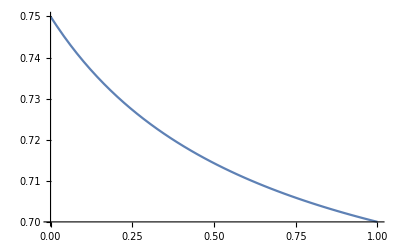

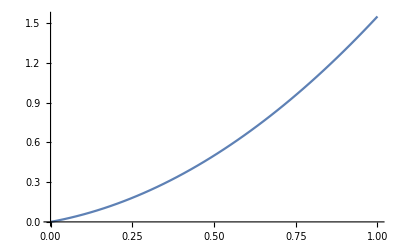

```mathematica
(* e *)
(* E(X|Y) (y)= integral x p(x|y) dx *)
EXpY[y_]=Simplify[Integrate[x*ppXpY[x,y],{x,0,1}]]
(* E(Y|X) (x)= integral y p(y|x) dy *)
EYpX[x_]=Simplify[Integrate[x*ppYpX[x,y],{y,0,1}]]

Plot[EXpY[y],{y,0,1}]
Plot[EYpX[x],{x,0,1}]
```

8. Slučajni spremenljivki X in Y sta neodvisni in enakomerno porazdeljeni na intervalu [0,1]. Naj bosta dani slučajni spremenljivki Z = max(X,Y) in U = X + Y. Zapišite gostote verjetnosti naslednjih porazdelitev
Z, U|Z, (Z,U), U, Z|U. Izračunajte verjetnost P(U>=1.5*Z).
Rezultat: 0.5.

If[z≥0,Piecewise[{{0, z<-1}, {2 z, -1<z<1}, {0, z>1}, {Indeterminate, True}}],0]

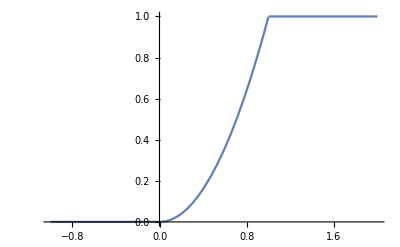

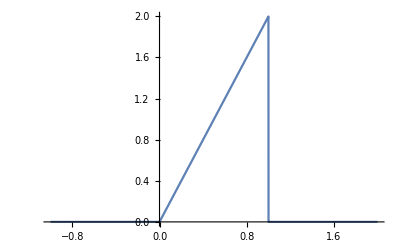

```mathematica
ClearAll["Global`*"]
FZ[z_]:=If[z≥0, Min[z^2,1],0]
pZ[z_]=D[FZ[z],z]
Plot[FZ[z],{z,-1,2}]
Plot[pZ[z],{z,-1,2}]
```

```mathematica
FpUpZ[u_,z_]:=Min[Max[(u-z)/z,0],1]
ppUpZ[u_,z_]=D[FpUpZ[u,z],u];
Plot3D[FpUpZ[u,z],{z,0,1},{u,0,2}]
Plot3D[ppUpZ[u,z],{z,0,1},{u,0,2}]
```

-Graphics3D-

-Graphics3D-

```mathematica
p[z_,u_]:=ppUpZ[u,z]*pZ[z];
Plot3D[p[z,u],{z,0,1},{u,0,2}]
```

-Graphics3D-

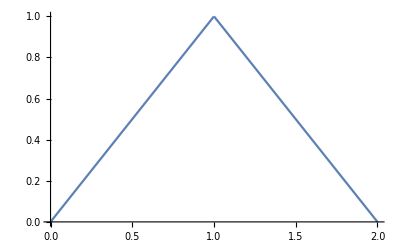

```mathematica
pU[u_]=Integrate[p[z,u],{z,0,1}];
Plot[pU[u],{u,0,2}]
```

```mathematica
ppZpU[z_,u_]=p[z,u]/pU[u];
Plot3D[ppZpU[z,u],{z,0,1},{u,0,2}]
```

-Graphics3D-

```mathematica
(* P(U≥1,5*z) *)
Integrate[p[z,u],{z,0,1},{u,1.5*z,2}]
```

0.5